## Телица Илья Денисович гр. 221701 Вариант 12

### Задание 1

```mathematica
f[x_,y_]=0.2 x^2+5*y^2;x0=0;y0=0.8;a=0;b=1;
h=0.1;n=(b-a)/h;
Koshi1=Table[1,{x,0,n},{y,1,2}];
Koshi1[[1,1]]=x0;
Koshi1[[1,2]]=y0;
(*Метод Эйлера для грубых значений*)
For[k=2,k<=n+1,k++,
Koshi1[[k,1]]=Koshi1[[k-1,1]]+h;
Koshi1[[k,2]]=Koshi1[[k-1,2]]+h*f[Koshi1[[k-1,1]],Koshi1[[k-1,2]]];
];

(*Уточнени метод Эйлера для метода Эйлера-Коши*)
For[k=2,k<=n+1,k++,
Koshi1[[k,2]]=Koshi1[[k-1,2]]+h/2*(f[Koshi1[[k-1,1]],Koshi1[[k-1,2]]]+f[Koshi1[[k,1]],Koshi1[[k,2]]]);
];
Koshi1Graph=ListPlot[Koshi1];



h=0.05;n=(b-a)/h;
Koshi2=Table[1,{x,0,n},{y,1,2}];
Koshi2[[1,1]]=x0;
Koshi2[[1,2]]=y0;
(*Метод Эйлера для грубых значений*)
For[k=2,k<=n+1,k++,
Koshi2[[k,1]]=Koshi2[[k-1,1]]+h;
Koshi2[[k,2]]=Koshi2[[k-1,2]]+h*f[Koshi2[[k-1,1]],Koshi2[[k-1,2]]];
];

(*Уточнени метод Эйлера для метода Эйлера-Коши*)
For[k=2,k<=n+1,k++,
Koshi2[[k,2]]=Koshi2[[k-1,2]]+h/2*(f[Koshi2[[k-1,1]],Koshi2[[k-1,2]]]+f[Koshi2[[k,1]],Koshi2[[k,2]]]);
];
Koshi2Graph=ListPlot[Koshi2];
Echo[Koshi1//TableForm,"Метод Эйлера-Коши для h=0.1"];
Show[Koshi1Graph]
Print[]
Print[]
Print[]
Echo[Koshi2//TableForm,"Метод Эйлера-Коши для h=0.05"];
Show[Koshi2Graph]
```

ListPlot::prng: Value of option PlotRange -> {{0,1.},{0,6.69893890070251×10^1292}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

Метод Эйлера-Коши для h=0.1  0 | 0.8
0.1 | 1.2737
0.2 | 2.44313
0.3 | 6.6179
0.4 | 36.2285
0.5 | 892.445
0.6 | 503685.
0.7 | 1.5598×10^11
0.8 | 1.4649×10^22
0.9 | 1.27033×10^44
1. | 9.41971×10^87

-Graphics-

Метод Эйлера-Коши для h=0.05  0 | 0.8
0.05 | 0.995213
0.1 | 1.29622
0.15 | 1.80471
0.2 | 2.78546
0.25 | 5.10776
0.3 | 12.8594
0.35 | 61.5568
0.4 | 1165.81
0.45 | 392905.
0.5 | 4.40539×10^10
0.55 | 5.49048×10^20
0.6 | 8.46389×10^40
0.65 | 1.99796×10^81
0.7 | 1.10672×10^162
0.75 | 3.37776591838628×10^323
0.8 | 3.13138006637622×10^646
0.85 | 2.679575560281×10^1292
0.9 | 1.95440342083145×10^2584
0.95 | 1.0359674736984×10^5168
1. | 2.90117986090084×10^10335

-Graphics-

```mathematica
h=0.1;n=(b-a)/h;
x=x0;y=y0;
Runge1=List[{x0,y0}];
For[k=1,k<=n,k++,
k1[x_,y_]:=h*f[x,y];
k2[x_,y_]:=h*f[x+h/2,y+k1[x,y]/2];
k3[x_,y_]:=h*f[x+h/2,y+k2[x,y]/2];
k4[x_,y_]:=h*f[x+h,y+k3[x,y]];
x=x+h;y=y+(k1[x,y]+2k2[x,y]+2k3[x,y]+k4[x,y])/6;
Runge1=Append[Runge1,{x,y}]]
Runge1Graph=ListPlot[Runge1];


h=0.05;n=(b-a)/h;
x=x0;y=y0;
Runge2=List[{x0,y0}];
For[k=1,k<=n,k++,
k1[x_,y_]:=h*f[x,y];
k2[x_,y_]:=h*f[x+h/2,y+k1[x,y]/2];
k3[x_,y_]:=h*f[x+h/2,y+k2[x,y]/2];
k4[x_,y_]:=h*f[x+h,y+k3[x,y]];
x=x+h;y=y+(k1[x,y]+2k2[x,y]+2k3[x,y]+k4[x,y])/6;
Runge2=Append[Runge2,{x,y}]]
Runge2Graph=ListPlot[Runge2];


Echo[Runge1//TableForm,"Метод Рунге-Кутта для h=0.1"];
Show[Runge1Graph]
Print[]
Print[]
Print[]
Echo[Runge1//TableForm,"Метод Рунге-Кутта для h=0.05"];
Show[Runge1Graph]
```

ListPlot::prng: Value of option PlotRange -> {{0,1.},{0,4.06892306688429×10^46424125}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

ListPlot::prng: Value of option PlotRange -> {{0,1.},{0,2.37507858325217829842593143109117093784`15.954589770191005*^189322902248246}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

Метод Рунге-Кутта для h=0.1  0 | 0.8
0.1 | 1.33224
0.2 | 3.82825
0.3 | 2293.22
0.4 | 7.3659×10^44
0.5 | 9.32514721257163×10^708
0.6 | 4.06003719178014×10^11334
0.7 | 6.76891495390836×10^181344
0.8 | 2.41181386611153×10^2901508
0.9 | 1.62756922675372×10^46424125
1. | 3.01072011493513×10^742785994

-Graphics-

Метод Рунге-Кутта для h=0.05  0 | 0.8
0.1 | 1.33224
0.2 | 3.82825
0.3 | 2293.22
0.4 | 7.3659×10^44
0.5 | 9.32514721257163×10^708
0.6 | 4.06003719178014×10^11334
0.7 | 6.76891495390836×10^181344
0.8 | 2.41181386611153×10^2901508
0.9 | 1.62756922675372×10^46424125
1. | 3.01072011493513×10^742785994

-Graphics-

```mathematica
Clear[x,y]
dsolve1=DSolve[{y'[x]==f[x,y[x]],y[x0]==y0},y[x],x];
dsolve1Func[x_]=y[x]/.Flatten[dsolve1];
dsolve1Graph=Plot[dsolveFunc[x],{x,a,b}];
Clear[x,y]
ndsolve1=NDSolve[{y'[x]==f[x,y[x]],y[x0]==y0},y[x],{x,a,b}];
ndsolve1Graph=Plot[Evaluate[y[x]/.ndsolve1],{x,a,b}];
Print["Метод DSolve"]
Show[dsolve1Graph]
Print["Метод NDSolve"]
Show[ndsolve1Graph]
```

NDSolve::ndsz: At x == 0.249967, step size is effectively zero; singularity or stiff system suspected.

Метод DSolve

-Graphics-

Метод NDSolve

-Graphics-

При уменьшении шага точность решение дифференциального уравнения возрастает

### Задание 2

Решения методом Эйлера для шага h=0.1

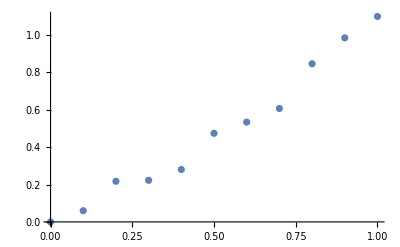

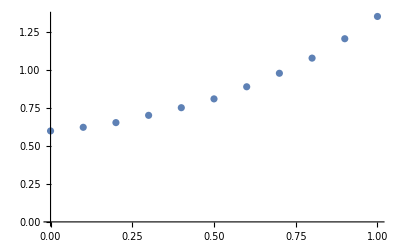

Решения методом Эйлера для шага h=0.05

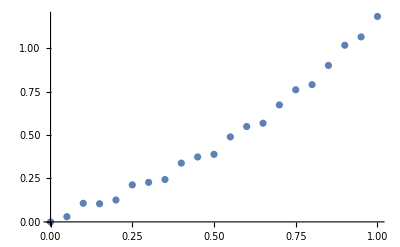

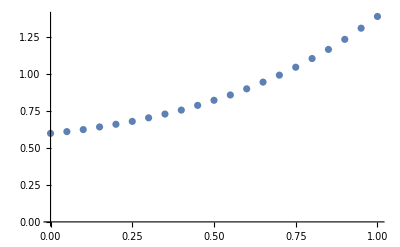

```mathematica
f[y_,z_,x_]=0.7*y+z+Sin[2*x];
g[y_,z_]=y+0.4*z;

x0=0;y[x0]=0;z[x0]=0.6;a=0;b=1;
h=0.1;n=(b-a)/h;
Do[
y[i+1]=y[i]+h*f[y[i],z[i],i];
z[i+1]=z[i]+h*g[y[i],z[i]];,{i,0,n}]

EulerYGraph1=ListPlot[Table[{i*h,y[i]},{i,0,n}]];
EulerZGraph1 = ListPlot[Table[{i*h,z[i]},{i,0,n}]];
h=0.05;n=(b-a)/h;
Do[
y[i+1]=y[i]+h*f[y[i],z[i],i];
z[i+1]=z[i]+h*g[y[i],z[i]];,{i,0,n}]

EulerYGraph2=ListPlot[Table[{i*h,y[i]},{i,0,n}]];
EulerZGraph2 = ListPlot[Table[{i*h,z[i]},{i,0,n}]];
Print["Решения методом Эйлера для шага h=0.1"]
Show[EulerYGraph1]
Show[EulerZGraph1]
Print["Решения методом Эйлера для шага h=0.05"]
Show[EulerYGraph2]
Show[EulerZGraph2]
```

Решения методом Ренге-Кутта для шага h=0.1

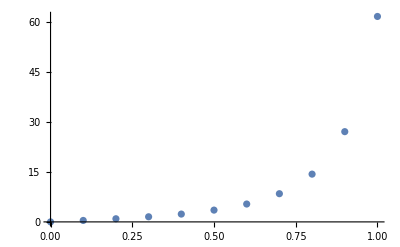

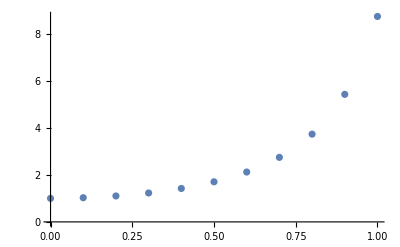

Решения методом Ренге-Кутта для шага h=0.05

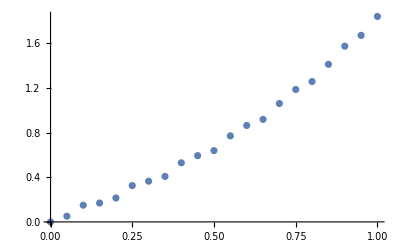

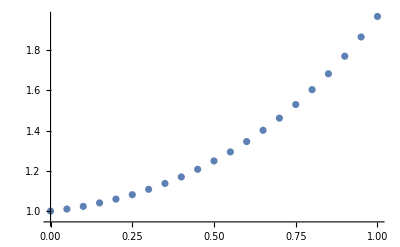

```mathematica
Clear[y,z];
y[x0]=0;z[x0]=1;
h=0.1;n=(b-a)/h;
Do[
k1=h*f[y[i],z[i],i];
l1=h*(y[i]-z[i]);
k2=h*f[y[i]+h/2,z[i]+l1/2];
l2=h*g[y[i]+h/2,z[i]+k1/2];
k3=h*f[y[i]+h/2,z[i]+l2/2];
l3=h*g[y[i]+h/2,z[i]+k2/2];
k4=h*f[y[i]+h,z[i]+l3];
l4=h*g[y[i]+h,z[i]+k3];
y[i+1]=y[i]+1/6*(k1+2*k2+2*k3+k4);
z[i+1]=z[i]+1/6*(l1+2*l2+2*l3+l4);,{i,0,n}]
RungeYGraph1=ListPlot[Table[{i*h,y[i]},{i,0,n}]];
RungeZGraph1=ListPlot[Table[{i*h,z[i]},{i,0,n}]];
h=0.05;n=(b-a)/h;
Do[
k1=h*f[y[i],z[i],i];
l1=h*(y[i]-z[i]);
k2=h*f[y[i]+h/2,z[i]+l1/2,i];
l2=h*g[y[i]+h/2,z[i]+k1/2];
k3=h*f[y[i]+h/2,z[i]+l2/2,i];
l3=h*g[y[i]+h/2,z[i]+k2/2];
k4=h*f[y[i]+h,z[i]+l3,i];
l4=h*g[y[i]+h,z[i]+k3];
y[i+1]=y[i]+1/6*(k1+2*k2+2*k3+k4);
z[i+1]=z[i]+1/6*(l1+2*l2+2*l3+l4);,{i,0,n}]
RungeYGraph2=ListPlot[Table[{i*h,y[i]},{i,0,n}]];
RungeZGraph2=ListPlot[Table[{i*h,z[i]},{i,0,n}]];
Print["Решения методом Ренге-Кутта для шага h=0.1"]
Show[RungeYGraph1]
Show[RungeZGraph1]
Print["Решения методом Ренге-Кутта для шага h=0.05"]
Show[RungeYGraph2]
Show[RungeZGraph2]
```

Решения методом DSolve

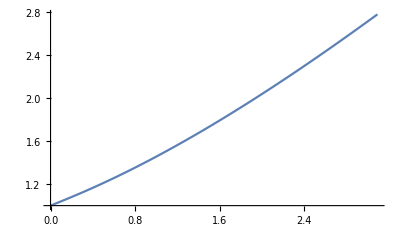

Решения методом NDSolve

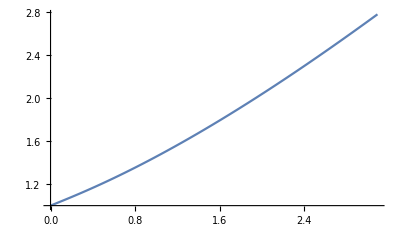

```mathematica
Clear[y,z];sol1=DSolve[{y'[x]==0.7*y[x]+z[x]+Sin[2*x],z'[x]==y[x]+0.4*z[x],y[0]==0,z[0]==1},{y,z},x];
sol2=NDSolve[{y'[x]==0.7*y[x]+z[x]+Sin[2*x],z'[x]==y[x]+0.4*z[x],y[0]==0,z[0]==1},{y,z},{x,a,b}];
DSolveGraph=ParametricPlot[Evaluate[{y[x],z[x]}/.sol1],{x,a,b}];
NDSolveGraph=ParametricPlot[Evaluate[{y[x],z[x]}/. sol2],{x,a,b}];
Print["Решения методом DSolve"]
Show[DSolveGraph]
Print["Решения методом NDSolve"]
Show[NDSolveGraph]
```